## Minimizing Variational Parameter for Donor in Center of Well

```mathematica
ClearAll["Global`*"]
t1=AbsoluteTime[];

dz=1;well=60.;border=200.;
lw=Floor[well/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];

x=0.1;
vmax=0.7*1.587*x;
v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
hom=7.62559/0.096;
ϵ=10.6*55.26349406*10^-4;

i1[λ_]:=(π*λ^2)/2.;
i4[λ_,z_]:=2.π*NIntegrate[s/(√(s^2+z^2))*ⅇ^(-2.*s/λ),{s,0,∞}]; 

λ=Range[40.,90., 2.5];
elist=0.0*λ;
Do[
α=i1[λ⟦j⟧];
i4λ=i4[λ⟦j⟧,z- (border+0.5*well) ];

energy=0.0;de=0.0005;
γ=-π/2.+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;ψmax=10.;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>10^-8,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;ψmax=10.;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];

elist⟦j⟧=energy;
,{j,Length[λ]}]

t2=AbsoluteTime[];
t2-t1
```

73.619431

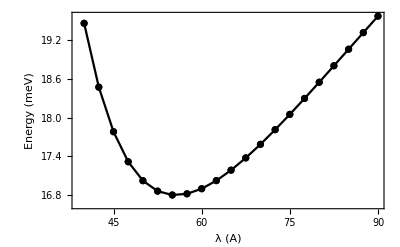

{16.8041,{55.}}

```mathematica
ListPlot[Table[{λ⟦i⟧,1000.*elist⟦i⟧},{i,Length[λ]}],Joined->True,Mesh->Full,PlotStyle->Black,Frame->True, FrameLabel->{"λ (A)","Energy (meV)"}]
{Min[elist]*1000,λ⟦Position[elist,Min[elist]]//Flatten⟧}
```

## Effect Of Donor Position on Ground State Energy and Bohr Radius (6 min)

```mathematica
ClearAll["Global`*"]
t1=AbsoluteTime[];

dz=1;well=60.;border=200.;
lw=Floor[well/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];

x=0.1;
vmax=0.7*1.587*x;
v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
hom=7.62559/0.096;
ϵ=10.6*55.26349406*10^-4;

i1[λ_]:=(π*λ^2)/2.;
i4[λ_,z_]:=2.π*NIntegrate[s/(√(s^2+z^2))*ⅇ^(-2.*s/λ),{s,0,∞}]; 

λ=0.;dλ=1.;
rd = Range[0.,220.,20.];
rd=Append[rd,230.];
bohrrad=elist=0.0*rd;
energy=100.;

Do[
energylast=energy=100;

While[energy≤energylast && λ < 250,
energylast=energy;
λ+=dλ;
α=i1[λ];
i4λ=i4[λ,z- rd ⟦-j⟧];

energy=0.0;de=0.005;
γ=-π/2.+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;ψmax=10.;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>10^-8,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;ψmax=10.;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy=energy-de;
];

elist⟦-j⟧=energylast;
bohrrad⟦-j⟧=λ-dλ;

,{j,Length[rd]}]

t2=AbsoluteTime[];
t2-t1
```

370.332704

## Ground State Energy Without Donor

```mathematica
energy=0.0;de=0.005;
γ=-π/2.-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;ψmax=10.;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>10^-8,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;ψmax=10.;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
enground=energy-de;
```

## Plots:

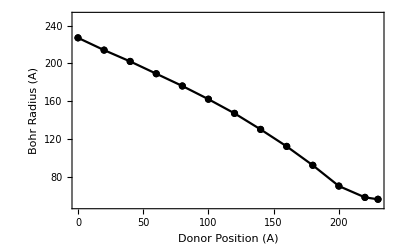

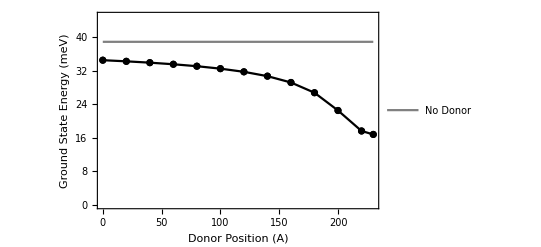

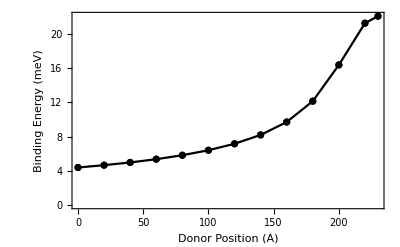

```mathematica
ListPlot[Table[{rd⟦i⟧,bohrrad⟦i⟧},{i,Length[rd]}],
PlotStyle->Black,Joined->True,Mesh->Full,Frame->True,FrameLabel->{"Donor Position (A)","Bohr Radius (A)"},PlotRange->{50,250}]

Show[
ListPlot[Table[{rd⟦i⟧,1000*elist⟦i⟧},{i,Length[rd]}],PlotRange->{0,45},
PlotStyle->Black,Joined->True,Mesh->Full,Frame->True,FrameLabel->{"Donor Position (A)","Ground State Energy (meV)"}],
ListPlot[Table[{rd⟦i⟧,1000*enground},{i,Length[rd]}],PlotStyle->Gray,Joined->True,PlotLegends->{"No Donor"}]
]

ListPlot[Table[{rd⟦i⟧,1000*(enground-elist⟦i⟧)},{i,Length[rd]}],
PlotStyle->Black,Joined->True,Mesh->Full,Frame->True,FrameLabel->{"Donor Position (A)","Binding Energy (meV)"}]
```

## Effect of Well Width on Ground Donor State (9 min)

## With Donor:

```mathematica
ClearAll["Global`*"]

t1=AbsoluteTime[];
well=Range[20.,400.,20.];
x=0.1;
vmax=0.7*1.587*x;
elist=bohrrad=0.0*well;
ψmax=100.;
tol=10^-8;

λ=1.;dλ=1.;
 i1[λ_]:=(π*λ^2)/2.;
i4[λ_,z_]:=2.π*NIntegrate[s/(√(s^2+z^2))*ⅇ^(-2.*s/λ),{s,0,∞}];

Do[

dz=1;border=200.;
lw=Floor[well⟦j⟧/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well⟦j⟧,dz];lz=Length[z];
rd = border+0.5*well⟦j⟧;


v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
hom=7.62559/0.096;
ϵ=10.6*55.26349406*10^-4;
energylast=energy=100;

α=i1[λ];
i4λ=i4[λ,z- rd ];

energy=-0.030;de=0.0001;
γ=-π/2.+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy1=energy-de;

λ+=dλ;

α=i1[λ];
i4λ=i4[λ,z- rd ];

energy=-0.030;de=0.0001;
γ=-π/2.+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy2=energy-de;

energy=energylast= Min[{energy1,energy2}];
If[energy2>energy1, dλ*=-1;λ+=dλ];

While[energy≤energylast && λ <200.,
energylast=energy;
λ+=dλ;
α=i1[λ];
i4λ=i4[λ,z- rd ];

energy=-0.030;de=0.0001;
γ=-π/2.+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy=energy-de;
];


elist⟦j⟧=energylast;
bohrrad⟦j⟧=λ-dλ;
,{j,Length[well]}]
t2=AbsoluteTime[];

(t2-t1)/60.
```

8.56599

## Without Donor:

```mathematica
well=Range[20.,400.,20.];
x=0.1;
vmax=0.7*1.587*x;
elist2=0.0*well;
 hom=7.62559/0.096;

Do[
dz=1;border=200.;
lw=Floor[well⟦j⟧/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well⟦j⟧,dz];lz=Length[z];
rd = border+0.5*well⟦j⟧;

v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
H=ConstantArray[0,{lz,lz}];
c=-hom/(2*dz^2);b=hom/dz^2+v;

H⟦1,{1,2}⟧ = {b⟦1⟧,c};
H⟦-1,{-1,-2}⟧ = {b⟦-1⟧,c};
Do[H⟦i,{i-1,i,i+1}⟧ = {c,b⟦i⟧,c};,{i,2,lz-1}];

elist2⟦j⟧=Sort[Eigenvalues[H]]⟦1⟧;
,{j,Length[well]}]
```

Plots:

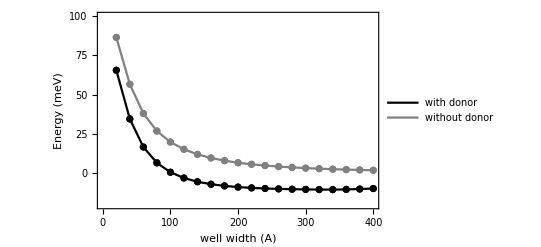

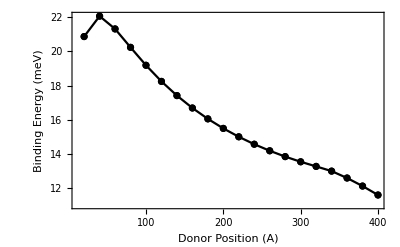

```mathematica
Show[
ListPlot[Table[{well⟦i⟧,1000*elist⟦i⟧},{i,Length[well]}],
PlotRange->{-20,100},Joined->True,Mesh->Full,PlotStyle->Black,PlotLegends->{"with donor"}],

ListPlot[Table[{well⟦i⟧,1000*elist2⟦i⟧},{i,Length[well]}],
PlotRange->{-20,100},Joined->True,Mesh->Full,PlotStyle->Gray,PlotLegends->{"without donor"}],
Frame->True,FrameLabel->{"well width (A)","Energy (meV)"}
]
ListPlot[Table[{well⟦i⟧,1000*(elist2⟦i⟧-elist⟦i⟧)},{i,Length[well]}],
PlotRange->All,Joined->True,Mesh->Full,PlotStyle->Black,
Frame->True,FrameLabel->{"Donor Position (A)","Binding Energy (meV)"}]
```